## Double pendulum time derivative Equation.

```mathematica
f={t,θ,φ,θdot,φdot}↦{
θdot,
φdot,
(-θdot^2 Cos[θ-φ]Sin[θ-φ]-φdot^2 Sin[θ-φ]-2Sin[θ]+Cos[θ-φ]Sin[φ])/(2-Cos[θ-φ]^2),
(2 θdot^2 Sin[θ-φ]+φdot^2 Sin[θ-φ]Cos[θ-φ]+2Cos[θ-φ]Sin[θ]-2Sin[φ])/(2-Cos[θ-φ]^2)
};
```

## RKF4(5) model

```mathematica
β={{2/9, 0, 0, 0, 0}, {1/12, 1/4, 0, 0, 0}, {69/128, -243/128, 135/64, 0, 0}, {-17/12, 27/4, -27/5, 16/15, 0}, {65/432, -5/16, 13/16, 4/27, 5/144}};
α=Total/@β;
c={1/9,0,9/20,16/45,1/12,0};
cHat={47/450,0,12/25,32/225,1/30,6/25};
cT=cHat-c;
rkf45prime={f,tol}↦Apply[{t,x,h}↦Module[
{f0,f1,f2,f3,f4,f5,xNext,xHat,hNext,TE},
f0=f[t,x];
f1=f[t+α⟦1⟧h,x+h(β⟦1,1⟧ f0)];
f2=f[t+α⟦2⟧h,x+h(β⟦2,1⟧ f0+β⟦2,2⟧ f1)];
f3=f[t+α⟦3⟧h,x+h(β⟦3,1⟧ f0+β⟦3,2⟧ f1+β⟦3,3⟧ f2)];
f4=f[t+α⟦4⟧h,x+h(β⟦4,1⟧ f0+β⟦4,2⟧ f1+β⟦4,3⟧ f2+β⟦4,4⟧ f3)];
f5=f[t+α⟦5⟧h,x+h(β⟦5,1⟧ f0+β⟦5,2⟧ f1+β⟦5,3⟧ f2+β⟦5,4⟧ f3+β⟦5,5⟧ f3)];
xNext=x+h(c⟦1⟧f0+c⟦2⟧f1+c⟦3⟧f2+c⟦4⟧f3+c⟦5⟧f4);
xHat=x+h(cHat⟦1⟧f0+cHat⟦2⟧f1+cHat⟦3⟧f2+cHat⟦4⟧f3+cHat⟦5⟧f4+cHat⟦6⟧f5);
TE=h(cT⟦1⟧f0+cT⟦2⟧f1+cT⟦3⟧f2+cT⟦4⟧f3+cT⟦5⟧f4+cT⟦6⟧f5);
hNext=0.9 h(tol/Max[Abs[TE]])^(1/5);
If[
Max[Abs[TE]]>tol,
{t,x,hNext,True},
{t+h,xHat,hNext,False}
]
]];
rkf45={f,tol}↦Module[{
stepPrime=rkf45prime[{t,x}↦f[t,Sequence@@x],tol]
},
Apply[{t,x,h}↦Most@NestWhile[stepPrime,{t,x,h,True},#⟦4⟧&]]
];
```

## Double pendulum time evolution with RKF4(5)

```mathematica
update=rkf45[f,10^-6];
state={0,{π/2,π/2,0,0},1};
update[state]
```

{0.149868,{1.55957,1.5708,-0.149855,-0.0000222426},0.149826}

```mathematica
wrap=θ↦Mod[θ+π,2π]-π
```

Function[θ,Mod[θ+π,2 π]-π]

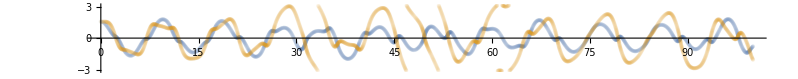

```mathematica
NestWhileList[update,state,#[[1]]<100&];
Transpose@Map[s↦{{s[[1]],wrap@s[[2,1]]},{s[[1]],wrap@s[[2,2]]}},%];
ListPlot[%,PlotStyle->Opacity[0.1],AspectRatio->1/10]
```

### Live animation (non-uniform timestep)

```mathematica
lp={s,colour}↦ListPlot[{{0,0},{Sin[s[[1]]],-Cos[s[[1]]]},{Sin[s[[1]]]+Sin[s[[2]]],-Cos[s[[1]]]-Cos[s[[2]]]}},Joined->True,Mesh->All,PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,MeshStyle->{PointSize[Large],colour},PlotStyle->colour];
```

```mathematica
pauseTime=(.1)/60.;
Dynamic@lp[state[[2]],Red]
Dynamic@state
While[True,state=update[state];Pause[pauseTime]];
```

$Aborted

## Doubled up pendula - differing initial conditions

```mathematica
doubleUp=f↦{t,s1,s2}↦{f[t,Sequence@@s1],f[t,Sequence@@s2]};
```

```mathematica
update=rkf45[doubleUp@f,10^-6];
state={0,{
{π/2,π/2,0,0},
{π/2,π/2(1+$MachineEpsilon),0,0}
},1};
update[state]
```

{0.149868,{{1.55957,1.5708,-0.149855,-0.0000222426},{1.55957,1.5708,-0.149855,-0.0000222426}},0.149826}

### Divergence of the smallest change in initial condition.

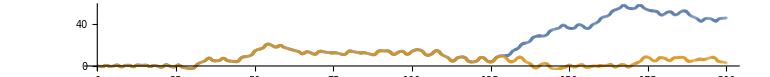

```mathematica
NestWhileList[update,state,#[[1]]<200&];
Transpose@Map[{
{#[[1]],#[[2,1,1]]-#[[2,1,2]]},
{#[[1]],#[[2,2,1]]-#[[2,2,2]]}
}&,%];
ListPlot[%,PlotStyle->Opacity[0.1],AspectRatio->1/10]
```

```mathematica
pauseTime=(.1)/60.;
Dynamic@Show[lp[state[[2,1]],Red],lp[state[[2,2]],Blue]]
Dynamic@state
While[True,state=update[state];Pause[pauseTime]];
```

$Aborted